```mathematica
Vector beam annular focusing simulation
```

```mathematica
Define parameters:
```

```mathematica
p=10;(*number of integration points*)
λ=1;(*wavelength*)
k=(2 π)/λ; (*wavenumber*)
Subscript[α, max]=1;(*inner angular extnet of annulus*)
Subscript[α, min]=0.75;(*outer angular extent of annulus*)
min=-2λ;max=2λ;step=100;(*transverse dimensions*)
zmin=-5λ;zmax=5λ;zstep=100;(*longitudinal dimensions*)
f=1λ;(*focal length*)
l0=1;(*peak field amplitude*)
A = (π f l0)/λ;(*constant before integration*)
β=1.5;(*ratio of pupil radius to beam waist AT ENTRANCE PUPIL*)
u[z_]:=k z Sin[Subscript[α, max]]^2;(*as defined in Richards & Wolf*)
v2d = Table[{k Sin[Subscript[α, max]] √(x^2+y^2),z},{x,Range[min,max,(max-min)/step]},{y,Range[min,max,(max-min)/step]},{z,Range[zmin,zmax,(zmax-zmin)/zstep]}];
v1d=Abs[Table[{k Sin[Subscript[α, max]] Range[min,max,(max-min)/step],z},{z,Range[zmin,zmax,(zmax-zmin)/zstep]}]];(*array with {v,z} value of each physical position*)
apod[θ_]:=Exp[-β^2 (Sin[θ]/Sin[Subscript[α, max]])^2] BesselJ[1,2 β Sin[θ]/Sin[Subscript[α, max]]];(*apodization function*)
```

```mathematica
Trapezoidal rule (1D)
```

```mathematica
RHO1d=Z1d=PHI1d=0*v1d;
RHO1d[[All,2]]=Z1d[[All,2]]=PHI1d[[All,2]]=v1d[[All,2]];
For[i=1,i<p,i++,RHO1d[[All,1]]=RHO1d[[All,1]]+(√Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*Sin[2(Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p)]*apod[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*BesselJ[1,v1d[[All,1]] Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]] *Exp[I u[RHO1d[[All,2]]] Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]^2]);
Z1d[[All,1]]=Z1d[[All,1]]+(√Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]^2*apod[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*BesselJ[0,v1d[[All,1]] Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]] *Exp[I u[Z1d[[All,2]]] Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]^2]);PHI1d[[All,1]]=PHI1d[[All,1]]+(√Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]* Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*apod[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*BesselJ[1,v1d[[All,1]] Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]] Exp[I u[PHI1d[[All,2]]] Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]^2])];

RHO1d[[All,1]]=A Subscript[α, max]/p(RHO1d[[All,1]]+(1/2 √Cos[Subscript[α, max]]*Sin[2 Subscript[α, max]]*apod[Subscript[α, max]]*BesselJ[1,v1d[[All,1]]]*Exp[I u[RHO1d[[All,2]]] Cos[Subscript[α, max]]/Sin[Subscript[α, max]]^2]));
Z1d[[All,1]]=2 I A Subscript[α, max]/p(Z1d[[All,1]]+(1/2 √Cos[Subscript[α, max]]*Sin[Subscript[α, max]]^2*apod[Subscript[α, max]]*BesselJ[0,v1d[[All,1]]]*Exp[I u[Z1d[[All,2]]] Cos[Subscript[α, max]]/Sin[Subscript[α, max]]^2]));
PHI1d[[All,1]]=2 A Subscript[α, max]/p (PHI1d[[All,1]]+(1/2 √Cos[Subscript[α, max]]*Sin[Subscript[α, max]]*apod[Subscript[α, max]]*BesselJ[1,v1d[[All,1]]]*Exp[I u[PHI1d[[All,2]]] Cos[Subscript[α, max]]/Sin[Subscript[α, max]]^2]));
```

```mathematica
Trapezoidal rule (2D)
```

```mathematica
RHO2d=Z2d=PHI2d=0*v2d;
RHO2d[[All,All,All,2]]=Z2d[[All,All,All,2]]=PHI2d[[All,All,All,2]]=v2d[[All,All,All,2]];
For[i=1,i<p,i++,RHO2d[[All,All,All,1]]=RHO2d[[All,All,All,1]]+(√Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*Sin[2(Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p)]*apod[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*BesselJ[1,v2d[[All,All,All,1]] Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]] *Exp[I u[RHO2d[[All,All,All,2]]] Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]^2]);
Z2d[[All,All,All,1]]=Z2d[[All,All,All,1]]+(√Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]^2*apod[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*BesselJ[0,v2d[[All,All,All,1]] Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]] *Exp[I u[Z2d[[All,All,All,2]]] Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]^2]);PHI2d[[All,All,All,1]]=PHI2d[[All,All,All,1]]+(√Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]* Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*apod[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]*BesselJ[1,v2d[[All,All,All,1]] Sin[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]] Exp[I u[PHI2d[[All,All,All,2]]] Cos[Subscript[α, min]+i (Subscript[α, max]-Subscript[α, min])/p]/Sin[Subscript[α, max]]^2])];

RHO2d[[All,All,All,1]]=A Subscript[α, max]/p(RHO2d[[All,All,All,1]]+(1/2 √Cos[Subscript[α, max]]*Sin[2 Subscript[α, max]]*apod[Subscript[α, max]]*BesselJ[1,v2d[[All,All,All,1]]]*Exp[I u[RHO2d[[All,All,All,2]]] Cos[Subscript[α, max]]/Sin[Subscript[α, max]]^2]));
Z2d[[All,All,All,1]]=2 I A Subscript[α, max]/p(Z2d[[All,All,All,1]]+(1/2 √Cos[Subscript[α, max]]*Sin[Subscript[α, max]]^2*apod[Subscript[α, max]]*BesselJ[0,v2d[[All,All,All,1]]]*Exp[I u[Z2d[[All,All,All,2]]] Cos[Subscript[α, max]]/Sin[Subscript[α, max]]^2]));
PHI2d[[All,All,All,1]]=2 A Subscript[α, max]/p (PHI2d[[All,All,All,1]]+(1/2 √Cos[Subscript[α, max]]*Sin[Subscript[α, max]]*apod[Subscript[α, max]]*BesselJ[1,v2d[[All,All,All,1]]]*Exp[I u[PHI2d[[All,All,All,2]]] Cos[Subscript[α, max]]/Sin[Subscript[α, max]]^2]));
```

```mathematica
Plots
```

```mathematica
Radial intensity (for chosen z position)
```

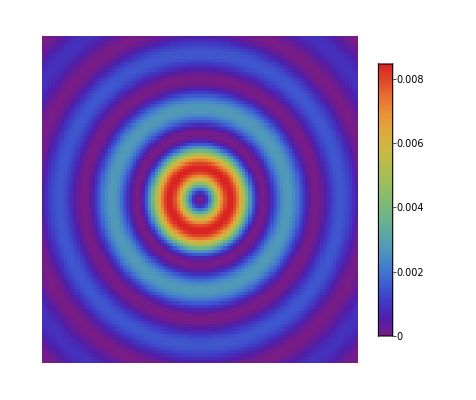

```mathematica
ArrayPlot[Abs[RHO2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

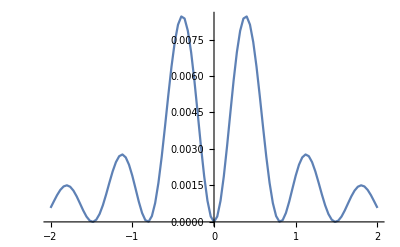

```mathematica
ListLinePlot[Abs[RHO1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Radial progagation
```

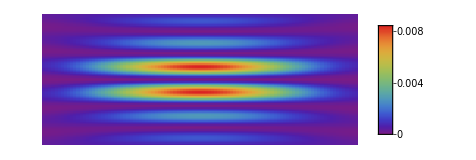

```mathematica
ArrayPlot[Abs[Transpose[RHO1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Longitudinal intensity (for chosen z position)
```

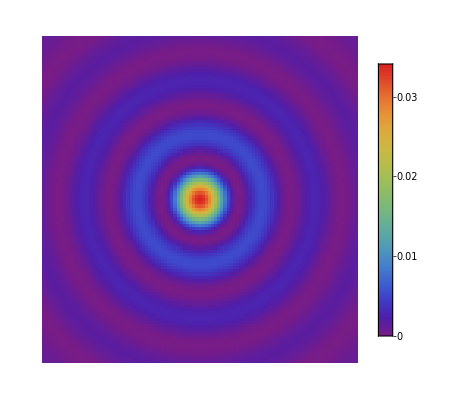

```mathematica
ArrayPlot[Abs[Z2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

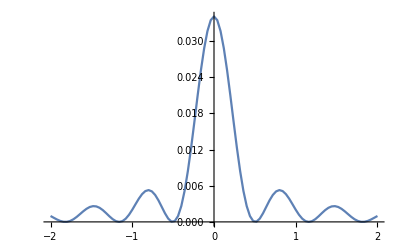

```mathematica
ListLinePlot[Abs[Z1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Longitudinal propagation
```

Longitudinal propagation

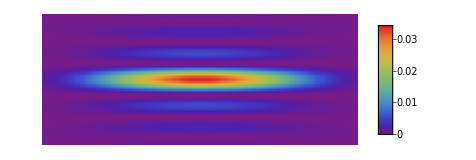

```mathematica
ArrayPlot[Abs[Transpose[Z1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

```mathematica
Azimuthal intensity (for chosen z position)
```

Azimuthal chosen for intensity position z

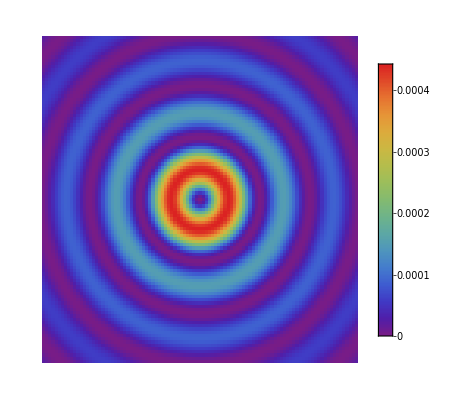

```mathematica
ArrayPlot[Abs[PHI2d[[All,All,51,1]]]^2,PlotLegends->Automatic,DataRange->{{min,max},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```

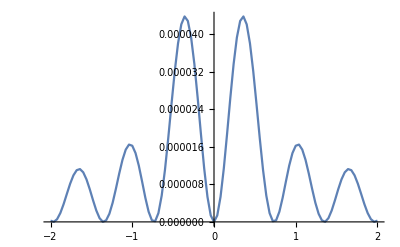

```mathematica
ListLinePlot[Abs[PHI1d[[51,1]]]^2,DataRange->{min,max},PlotRange->All]
```

```mathematica
Azimuthal propagation
```

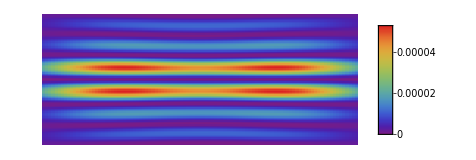

```mathematica
ArrayPlot[Abs[Transpose[PHI1d[[All,1]]]]^2,PlotLegends->Automatic,DataRange->{{zmin,zmax},{min,max}},FrameTicks->All,ColorFunction->"Rainbow"]
```